-Graphics-

-Graphics-
A | = | -Graphics-
A∖B | + | -Graphics-
A∩B
-Graphics-
A | + | -Graphics-
B | = | -Graphics-
A∪B | + | -Graphics-
A∩B

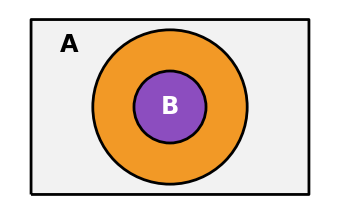
-Graphics-
-Graphics-
A | = | -Graphics-
A∖B | + | -Graphics-
B

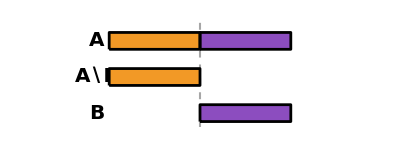
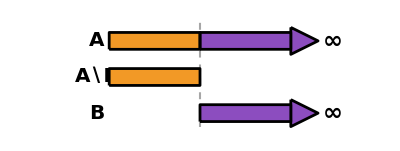
A y B finitos
-Graphics-B infinito → A infinito
-Graphics-

```mathematica
ClearAll[x, y, sepV, rV, limXV, limYV, enA, enB, region, colReg, vennGrande, diagrama1];

sepV = 0.7; rV = 1.2; limXV = 2.7; limYV = 1.7;

enA = (x + sepV)^2 + y^2 < rV^2;
enB = (x - sepV)^2 + y^2 < rV^2;

region[1] = enA && ! enB;   (* A\B *)
region[2] = enA && enB;     (* A∩B *)
region[3] = ! enA && enB;   (* B\A *)

colReg = {RGBColor[0.95, 0.6, 0.15], RGBColor[0.55, 0.3, 0.75], RGBColor[0.2, 0.55, 0.85]};

vennGrande = Show[
   Graphics[{GrayLevel[0.95], Rectangle[{-limXV, -limYV}, {limXV, limYV}]}],
   Sequence @@ Table[
     RegionPlot[Evaluate[region[k]], {x, -limXV, limXV}, {y, -limYV, limYV},
      PlotStyle -> Directive[colReg[[k]], Opacity[0.9]], BoundaryStyle -> None,
      PlotPoints -> 60, MaxRecursion -> 3],
     {k, 1, 3}],
   Graphics[{FaceForm[None], EdgeForm[{Black, AbsoluteThickness[2]}],
     Rectangle[{-limXV, -limYV}, {limXV, limYV}],
     Black, AbsoluteThickness[2], Circle[{-sepV, 0}, rV], Circle[{sepV, 0}, rV],
     Text[Style["A", 24, Bold], {-sepV - rV + 0.25, rV - 0.1}],
     Text[Style["B", 24, Bold], {sepV + rV - 0.25, rV - 0.1}]}],
   PlotRange -> {{-limXV, limXV}, {-limYV, limYV}}, AspectRatio -> Automatic,
   Frame -> False, Axes -> False, ImageSize -> 420];

diagrama1 = Legended[vennGrande,
   SwatchLegend[colReg, {"A∖B", "A∩B", "B∖A"},
    LabelStyle -> Directive[FontSize -> 17], LegendMarkerSize -> 20]];
ClearAll[x, y, sepV, rV, limXV, limYV, enA, enB, region, colReg, miniVenn, elem, signo, fila1, fila2, diagrama2];

sepV = 0.7; rV = 1.2; limXV = 2.7; limYV = 1.7;

enA = (x + sepV)^2 + y^2 < rV^2;
enB = (x - sepV)^2 + y^2 < rV^2;

region[1] = enA && ! enB;
region[2] = enA && enB;
region[3] = ! enA && enB;

colReg = {RGBColor[0.95, 0.6, 0.15], RGBColor[0.55, 0.3, 0.75], RGBColor[0.2, 0.55, 0.85]};

(* mini Venn que colorea solo las regiones indicadas en inc *)
miniVenn[inc_List, tam_: 130] := Show[
   Graphics[{GrayLevel[0.95], Rectangle[{-limXV, -limYV}, {limXV, limYV}]}],
   Sequence @@ Table[
     RegionPlot[Evaluate[region[k]], {x, -limXV, limXV}, {y, -limYV, limYV},
      PlotStyle -> Directive[colReg[[k]], Opacity[0.9]], BoundaryStyle -> None,
      PlotPoints -> 40, MaxRecursion -> 2],
     {k, inc}],
   Graphics[{FaceForm[None], EdgeForm[{Black, AbsoluteThickness[1.5]}],
     Rectangle[{-limXV, -limYV}, {limXV, limYV}],
     Black, AbsoluteThickness[1.5], Circle[{-sepV, 0}, rV], Circle[{sepV, 0}, rV]}],
   PlotRange -> {{-limXV, limXV}, {-limYV, limYV}}, AspectRatio -> Automatic,
   Frame -> False, Axes -> False, ImageSize -> tam];

elem[inc_List, etq_] := Column[{miniVenn[inc], Style[etq, 18, Bold]},
   Alignment -> Center, Spacings -> 0.3];
signo[s_] := Style[s, 32, Bold, GrayLevel[0.4]];

(* propiedad 1: A = (A\B) + (A∩B) *)
fila1 = Grid[{{elem[{1, 2}, "A"], signo["="], elem[{1}, "A∖B"], signo["+"],
     elem[{2}, "A∩B"]}},
   Alignment -> Center, Spacings -> {1.2, 0}];

(* propiedad 2: A + B = (A∪B) + (A∩B); el morado aparece dos veces a cada lado *)
fila2 = Grid[{{elem[{1, 2}, "A"], signo["+"], elem[{2, 3}, "B"], signo["="],
     elem[{1, 2, 3}, "A∪B"], signo["+"], elem[{2}, "A∩B"]}},
   Alignment -> Center, Spacings -> {1.2, 0}];

diagrama2 = Column[{fila1, fila2}, Alignment -> Center, Spacings -> 2];

ClearAll[colRing, colBall, nido, elem, signo, nidoGrande, fila, diagrama3];

colRing = RGBColor[0.95, 0.6, 0.15];   (* A\B *)
colBall = RGBColor[0.55, 0.3, 0.75];   (* B = A∩B, porque B está dentro de A *)

nido[ring_, ball_, tam_: 130, etq_: False] := Graphics[{
    {GrayLevel[0.95], Rectangle[{-2.7, -1.7}, {2.7, 1.7}]},
    {If[ring, colRing, GrayLevel[0.95]], Disk[{0, 0}, 1.5]},
    {If[ball, colBall, GrayLevel[0.95]], Disk[{0, 0}, 0.7]},
    {Black, AbsoluteThickness[2], Circle[{0, 0}, 1.5], Circle[{0, 0}, 0.7]},
    {FaceForm[None], EdgeForm[{Black, AbsoluteThickness[2]}], Rectangle[{-2.7, -1.7}, {2.7, 1.7}]},
    If[etq, {Black, Text[Style["A", 24, Bold], {-1.95, 1.2}],
      Text[Style["B", 24, Bold, White], {0, 0}]}, {}]},
   PlotRange -> {{-2.7, 2.7}, {-1.7, 1.7}}, ImageSize -> tam];

elem[ring_, ball_, etq_] := Column[{nido[ring, ball], Style[etq, 18, Bold]},
   Alignment -> Center, Spacings -> 0.3];
signo[s_] := Style[s, 32, Bold, GrayLevel[0.4]];

nidoGrande = nido[True, True, 340, True];

(* A = (A\B) + B  ->  A\B = A - B cuando B es finito *)
fila = Grid[{{elem[True, True, "A"], signo["="], elem[True, False, "A∖B"],
     signo["+"], elem[False, True, "B"]}},
   Alignment -> Center, Spacings -> {1.2, 0}];

diagrama3 = Column[{nidoGrande, fila}, Alignment -> Center, Spacings -> 2];
ClearAll[colO, colP, h, barra, punta, panelBarras, panelFin, panelInf, diagrama4];

colO = RGBColor[0.95, 0.6, 0.15];   (* A\B *)
colP = RGBColor[0.55, 0.3, 0.75];   (* B *)
h = 0.28;

barra[x1_, x2_, y_, col_] := {col, EdgeForm[{Black, AbsoluteThickness[2]}],
   Rectangle[{x1, y - h}, {x2, y + h}]};
punta[x_, y_, col_] := {col, EdgeForm[{Black, AbsoluteThickness[2]}],
   Polygon[{{x, y + 1.6 h}, {x, y - 1.6 h}, {x + 0.9, y}}]};

(* tres barras alineadas: A arriba, y debajo A\B y B en su sitio *)
panelBarras[inf_, titulo_] := Module[{yA = 0, yO = -1.2, yB = -2.4},
   Column[{
     Style[titulo, 20, Bold],
     Graphics[{
       {GrayLevel[0.65], Dashed, AbsoluteThickness[1.5],
        Line[{{3, yA + 0.6}, {3, yB - 0.6}}]},
       barra[0, 3, yA, colO], barra[3, 6, yA, colP],
       If[inf, {punta[6, yA, colP], Text[Style["∞", 24, Bold], {7.4, yA}]}, {}],
       barra[0, 3, yO, colO],
       barra[3, 6, yB, colP],
       If[inf, {punta[6, yB, colP], Text[Style["∞", 24, Bold], {7.4, yB}]}, {}],
       Black,
       Text[Style["A", 20, Bold], {-0.4, yA}, {1, 0}],
       Text[Style["A∖B", 20, Bold], {-0.4, yO}, {1, 0}],
       Text[Style["B", 20, Bold], {-0.4, yB}, {1, 0}]},
      PlotRange -> {{-2.4, 8.4}, {yB - 0.8, yA + 0.9}}, ImageSize -> 400]},
    Alignment -> Center, Spacings -> 0.5]
   ];

panelFin = panelBarras[False, "A y B finitos"];
panelInf = panelBarras[True, "B infinito → A infinito"];

diagrama4 = Row[{panelFin, Spacer[40], panelInf}];

diagrama1
diagrama2
diagrama3
diagrama4
```

```mathematica
Export[CloudObject["T2_1_a.png"], diagrama1, "PNG", Background -> None, ImageResolution -> 300, ImageSize -> 700]
Export[CloudObject["T2_1_b.png"], diagrama2, "PNG", Background -> None, ImageResolution -> 300, ImageSize -> 700]
Export[CloudObject["T2_1_c.png"], diagrama3, "PNG", Background -> None, ImageResolution -> 300, ImageSize -> 700]
Export[CloudObject["T2_1_d.png"], diagrama4, "PNG", Background -> None, ImageResolution -> 300, ImageSize -> 700]
```

CloudObject[https://www.wolframcloud.com/obj/jesusparejop/T2_1_a.png]

CloudObject[https://www.wolframcloud.com/obj/jesusparejop/T2_1_b.png]

CloudObject[https://www.wolframcloud.com/obj/jesusparejop/T2_1_c.png]

CloudObject[https://www.wolframcloud.com/obj/jesusparejop/T2_1_d.png]

-Graphics-
A_1 | ⊂ | -Graphics-
A_2 | ⊂ | -Graphics-
A_k | ⊂ | -Graphics-
A_(k+1) | ⊂ | ⋯ | → | -Graphics-
lim A_n

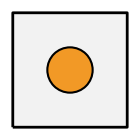
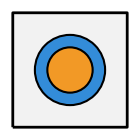
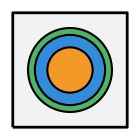
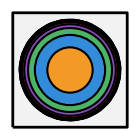
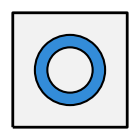
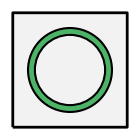
-Graphics-
A_1 | ⊂ | -Graphics-
A_2 | ⊂ | -Graphics-
A_3 | ⊂ | ⋯ | → | -Graphics-
lim A_n
-Graphics-
B_1 | ⊔ | -Graphics-
B_2 | ⊔ | -Graphics-
B_3 | ⊔ | ⋯ | = | -Graphics-
∪ B_i

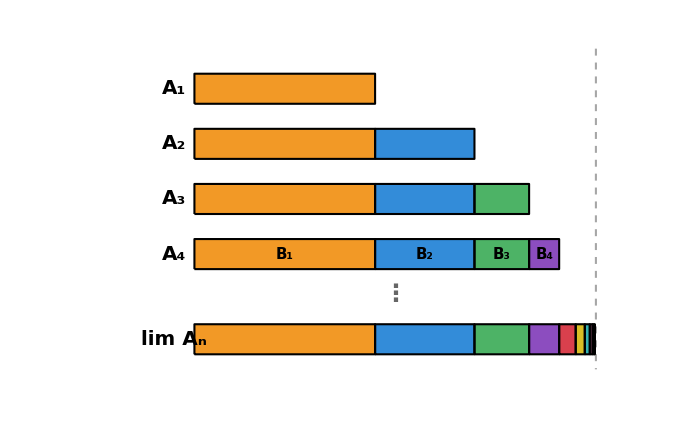

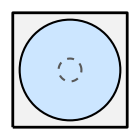
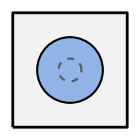
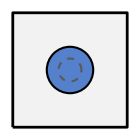
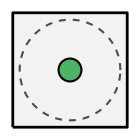
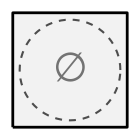
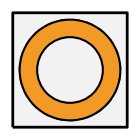
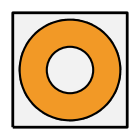
-Graphics-
A_k | ⊃ | -Graphics-
A_(k+1) | ⊃ | -Graphics-
A_(k+2) | ⊃ | ⋯ | → | -Graphics-
∩ A_n
-Graphics-
B_1 | ⊂ | -Graphics-
B_2 | ⊂ | -Graphics-
B_3 | ⊂ | ⋯ | → | -Graphics-
A_k∖ lim A_n

```mathematica
ClearAll[rad, colAzul, colRojo, marco, borde, kInf, panelN, panelLim, conEtq, signo, cuerpo, diagrama1];

rad[n_] := 2.2 (1 - 0.55^n);   (* A_n son discos concéntricos que crecen *)
colAzul = RGBColor[0.55, 0.75, 0.95];
colRojo = RGBColor[0.85, 0.25, 0.3];
kInf = 3;   (* primer índice con medida infinita *)

marco = {GrayLevel[0.95], Rectangle[{-2.5, -2.5}, {2.5, 2.5}]};
borde = {FaceForm[None], EdgeForm[{Black, AbsoluteThickness[2]}], Rectangle[{-2.5, -2.5}, {2.5, 2.5}]};

panelN[n_] := Graphics[{marco,
    {If[n ≥ kInf, colRojo, colAzul], Disk[{0, 0}, rad[n]]},
    {Black, AbsoluteThickness[1.5], Circle[{0, 0}, rad[n]]},
    If[n ≥ kInf, Text[Style["∞", 44, Bold, White], {0, 0}], {}],
    borde},
   PlotRange -> {{-2.5, 2.5}, {-2.5, 2.5}}, ImageSize -> 130];

(* el límite contiene a A_k, que ya es infinito *)
panelLim = Graphics[{marco,
    {colRojo, Disk[{0, 0}, 2.2]},
    {Black, AbsoluteThickness[1.5], Dashed, Circle[{0, 0}, 2.2]},
    {Black, AbsoluteThickness[3], Circle[{0, 0}, rad[kInf]]},
    Text[Style["∞", 44, Bold, White], {0, 0}],
    Text[Style[Subscript["A", "k"], 20, Bold, White], {0, -rad[kInf] + 0.35}],
    borde},
   PlotRange -> {{-2.5, 2.5}, {-2.5, 2.5}}, ImageSize -> 130];

conEtq[g_, txt_] := Column[{g, Style[txt, 20, Bold]}, Alignment -> Center, Spacings -> 0.3];
signo[s_] := Style[s, 28, Bold, GrayLevel[0.4]];

cuerpo = Grid[{{
    conEtq[panelN[1], Subscript["A", 1]], signo["⊂"],
    conEtq[panelN[2], Subscript["A", 2]], signo["⊂"],
    conEtq[panelN[3], Subscript["A", "k"]], signo["⊂"],
    conEtq[panelN[4], Subscript["A", "k+1"]], signo["⊂"],
    signo["⋯"], signo["→"],
    conEtq[panelLim, Row[{"lim ", Subscript["A", "n"]}]]}},
   Alignment -> Center, Spacings -> {0.8, 0}];

diagrama1 = Legended[cuerpo,
   SwatchLegend[{colAzul, colRojo}, {"medida finita", "medida infinita"},
    LabelStyle -> Directive[FontSize -> 16], LegendMarkerSize -> 20]];
ClearAll[rad, colR, marco, borde, anillos, panelA, panelB, panelLim, conEtq, signo, diagrama2];

rad[n_] := 2.2 (1 - 0.55^n);   (* radios de los discos A_n, crecen hacia 2.2 *)
colR = {RGBColor[0.95, 0.6, 0.15], RGBColor[0.2, 0.55, 0.85], RGBColor[0.3, 0.7, 0.4],
   RGBColor[0.55, 0.3, 0.75], RGBColor[0.85, 0.25, 0.3], RGBColor[0.85, 0.75, 0.15],
   RGBColor[0.2, 0.7, 0.7], RGBColor[0.9, 0.5, 0.7]};

marco = {GrayLevel[0.95], Rectangle[{-2.5, -2.5}, {2.5, 2.5}]};
borde = {FaceForm[None], EdgeForm[{Black, AbsoluteThickness[2]}], Rectangle[{-2.5, -2.5}, {2.5, 2.5}]};

(* disco A_n coloreado por coronas: B_1 (centro), B_2, ..., B_n *)
anillos[nMax_] := {
   Table[{colR[[Mod[k - 1, 8] + 1]], Disk[{0, 0}, rad[k]]}, {k, nMax, 1, -1}],
   Table[{Black, AbsoluteThickness[1.5], Circle[{0, 0}, rad[k]]}, {k, 1, nMax}]};

panelA[n_] := Graphics[{marco, anillos[n], borde},
   PlotRange -> {{-2.5, 2.5}, {-2.5, 2.5}}, ImageSize -> 140];

(* solo la corona B_n = A_n \ A_(n-1) *)
panelB[n_] := Graphics[{marco,
    {colR[[n]], Disk[{0, 0}, rad[n]]},
    If[n > 1, {GrayLevel[0.95], Disk[{0, 0}, rad[n - 1]]}, {}],
    {Black, AbsoluteThickness[1.5], Circle[{0, 0}, rad[n]]},
    If[n > 1, {Black, AbsoluteThickness[1.5], Circle[{0, 0}, rad[n - 1]]}, {}],
    borde},
   PlotRange -> {{-2.5, 2.5}, {-2.5, 2.5}}, ImageSize -> 140];

(* el límite: todas las coronas juntas *)
panelLim = Graphics[{marco, anillos[10],
    {Black, AbsoluteThickness[1.5], Dashed, Circle[{0, 0}, 2.2]}, borde},
   PlotRange -> {{-2.5, 2.5}, {-2.5, 2.5}}, ImageSize -> 140];

conEtq[g_, txt_] := Column[{g, Style[txt, 20, Bold]}, Alignment -> Center, Spacings -> 0.3];
signo[s_] := Style[s, 28, Bold, GrayLevel[0.4]];

diagrama2 = Grid[{
    {conEtq[panelA[1], Subscript["A", 1]], signo["⊂"],
     conEtq[panelA[2], Subscript["A", 2]], signo["⊂"],
     conEtq[panelA[3], Subscript["A", 3]], signo["⊂"],
     signo["⋯"], signo["→"],
     conEtq[panelLim, Row[{"lim ", Subscript["A", "n"]}]]},
    {conEtq[panelB[1], Subscript["B", 1]], signo["⊔"],
     conEtq[panelB[2], Subscript["B", 2]], signo["⊔"],
     conEtq[panelB[3], Subscript["B", 3]], signo["⊔"],
     signo["⋯"], signo["="],
     conEtq[panelLim, Row[{"∪ ", Subscript["B", "i"]}]]}},
   Alignment -> Center, Spacings -> {0.8, 2}];
ClearAll[L, colR, h, barraApilada, nFilas, dy, filas, etiquetasB, yPuntos, yLim, diagrama3];

L[n_] := If[n == 0, 0, 8 (1 - 0.55^n)];   (* longitud de A_n = suma de las longitudes B_1..B_n *)
colR = {RGBColor[0.95, 0.6, 0.15], RGBColor[0.2, 0.55, 0.85], RGBColor[0.3, 0.7, 0.4],
   RGBColor[0.55, 0.3, 0.75], RGBColor[0.85, 0.25, 0.3], RGBColor[0.85, 0.75, 0.15],
   RGBColor[0.2, 0.7, 0.7], RGBColor[0.9, 0.5, 0.7]};
h = 0.3; nFilas = 4; dy = 1.1;

(* barra de A_n: segmentos B_1, ..., B_n puestos uno a continuación de otro *)
barraApilada[n_, y_] := Table[
   {colR[[Mod[k - 1, 8] + 1]], EdgeForm[{Black, AbsoluteThickness[1.5]}],
    Rectangle[{L[k - 1], y - h}, {L[k], y + h}]},
   {k, 1, n}];

filas = Table[
   {barraApilada[n, -(n - 1) dy],
    Text[Style[Subscript["A", n], 20, Bold], {-0.4, -(n - 1) dy}, {1, 0}]},
   {n, 1, nFilas}];

(* nombres de los segmentos, sobre la última fila *)
etiquetasB = Table[
   Text[Style[Subscript["B", k], 15, Bold], {(L[k - 1] + L[k])/2, -(nFilas - 1) dy}],
   {k, 1, nFilas}];

yPuntos = -(nFilas - 1) dy - 0.8;
yLim = -(nFilas - 1) dy - 1.7;

diagrama3 = Graphics[{
    {GrayLevel[0.65], Dashed, AbsoluteThickness[1.5], Line[{{8, 0.8}, {8, yLim - 0.6}}]},
    filas, etiquetasB,
    Text[Style["⋮", 24, Bold, GrayLevel[0.4]], {4, yPuntos}],
    barraApilada[10, yLim],
    Text[Style[Row[{"lim ", Subscript["A", "n"]}], 20, Bold], {-0.4, yLim}, {1, 0}]},
   PlotRange -> {{-2.6, 8.8}, {yLim - 0.9, 1.0}}, ImageSize -> 700];
ClearAll[s, colA, colB, colLim, marco, borde, discoA, anilloB, panelLimA, panelLimB, conEtq, signo, diagrama4];

s[j_] := 0.5 + 1.7 0.55^(j - 1);   (* radios decrecientes de A_k, A_(k+1), ... hacia 0.5 *)
colA[j_] := Blend[{RGBColor[0.8, 0.9, 1], RGBColor[0.1, 0.3, 0.7]}, (j - 1)/3];
colB = RGBColor[0.95, 0.6, 0.15];
colLim = RGBColor[0.3, 0.7, 0.4];

marco = {GrayLevel[0.95], Rectangle[{-2.5, -2.5}, {2.5, 2.5}]};
borde = {FaceForm[None], EdgeForm[{Black, AbsoluteThickness[2]}], Rectangle[{-2.5, -2.5}, {2.5, 2.5}]};

(* fila de arriba: discos que se encogen; el círculo discontinuo marca el límite *)
discoA[j_] := Graphics[{marco,
    {colA[j], Disk[{0, 0}, s[j]]},
    {Black, AbsoluteThickness[1.5], Circle[{0, 0}, s[j]]},
    {GrayLevel[0.35], Dashed, AbsoluteThickness[1.5], Circle[{0, 0}, 0.5]},
    borde},
   PlotRange -> {{-2.5, 2.5}, {-2.5, 2.5}}, ImageSize -> 140];

(* fila de abajo: B_j = A_k menos A_(j+k-1), una corona que crece (B_1 es vacío) *)
anilloB[j_] := Graphics[{marco,
    {GrayLevel[0.3], Dashed, AbsoluteThickness[1.5], Circle[{0, 0}, s[1]]},
    If[j > 1,
     {{colB, Disk[{0, 0}, s[1]]}, {GrayLevel[0.95], Disk[{0, 0}, s[j]]},
      {Black, AbsoluteThickness[1.5], Circle[{0, 0}, s[1]], Circle[{0, 0}, s[j]]}},
     Text[Style["∅", 40, GrayLevel[0.45]], {0, 0}]],
    borde},
   PlotRange -> {{-2.5, 2.5}, {-2.5, 2.5}}, ImageSize -> 140];

(* límites: la intersección (disco pequeño) y A_k menos ese disco (corona completa) *)
panelLimA = Graphics[{marco,
    {GrayLevel[0.3], Dashed, AbsoluteThickness[1.5], Circle[{0, 0}, s[1]]},
    {colLim, Disk[{0, 0}, 0.5]},
    {Black, AbsoluteThickness[1.5], Circle[{0, 0}, 0.5]},
    borde},
   PlotRange -> {{-2.5, 2.5}, {-2.5, 2.5}}, ImageSize -> 140];

panelLimB = Graphics[{marco,
    {colB, Disk[{0, 0}, s[1]]}, {GrayLevel[0.95], Disk[{0, 0}, 0.5]},
    {Black, AbsoluteThickness[1.5], Circle[{0, 0}, s[1]]},
    {colLim, AbsoluteThickness[3], Circle[{0, 0}, 0.5]},
    borde},
   PlotRange -> {{-2.5, 2.5}, {-2.5, 2.5}}, ImageSize -> 140];

conEtq[g_, txt_] := Column[{g, Style[txt, 20, Bold]}, Alignment -> Center, Spacings -> 0.3];
signo[s_] := Style[s, 28, Bold, GrayLevel[0.4]];

diagrama4 = Grid[{
    {conEtq[discoA[1], Subscript["A", "k"]], signo["⊃"],
     conEtq[discoA[2], Subscript["A", "k+1"]], signo["⊃"],
     conEtq[discoA[3], Subscript["A", "k+2"]], signo["⊃"],
     signo["⋯"], signo["→"],
     conEtq[panelLimA, Row[{"∩ ", Subscript["A", "n"]}]]},
    {conEtq[anilloB[1], Subscript["B", 1]], signo["⊂"],
     conEtq[anilloB[2], Subscript["B", 2]], signo["⊂"],
     conEtq[anilloB[3], Subscript["B", 3]], signo["⊂"],
     signo["⋯"], signo["→"],
     conEtq[panelLimB, Row[{Subscript["A", "k"], "∖ ", "lim ", Subscript["A", "n"]}]]}},
   Alignment -> Center, Spacings -> {0.8, 2}];

diagrama1
diagrama2
diagrama3
diagrama4
```

```mathematica
Export[CloudObject["T2_1_e.png"], diagrama1, "PNG", Background -> None, ImageResolution -> 300, ImageSize -> 700]
Export[CloudObject["T2_1_f.png"], diagrama2, "PNG", Background -> None, ImageResolution -> 300, ImageSize -> 700]
Export[CloudObject["T2_1_g.png"], diagrama3, "PNG", Background -> None, ImageResolution -> 300, ImageSize -> 700]
Export[CloudObject["T2_1_h.png"], diagrama4, "PNG", Background -> None, ImageResolution -> 300, ImageSize -> 700]
```

CloudObject[https://www.wolframcloud.com/obj/jesusparejop/T2_1_e.png]

CloudObject[https://www.wolframcloud.com/obj/jesusparejop/T2_1_f.png]

CloudObject[https://www.wolframcloud.com/obj/jesusparejop/T2_1_g.png]

CloudObject[https://www.wolframcloud.com/obj/jesusparejop/T2_1_h.png]

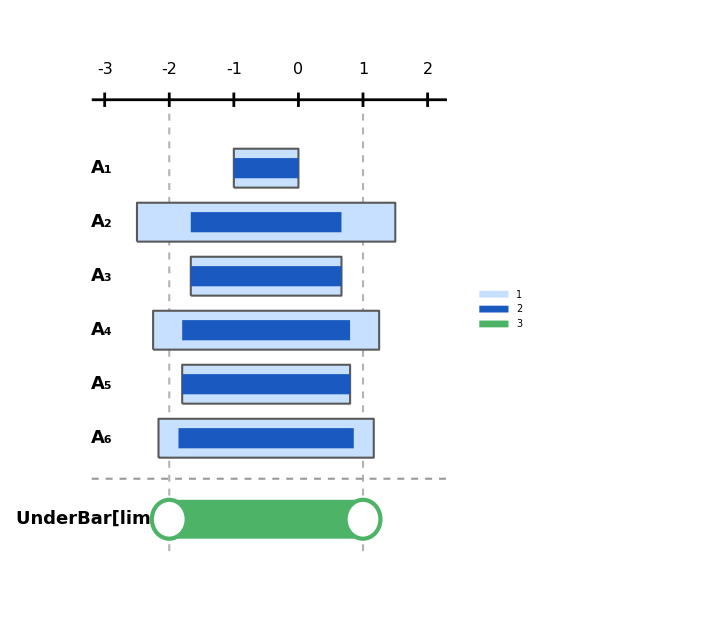

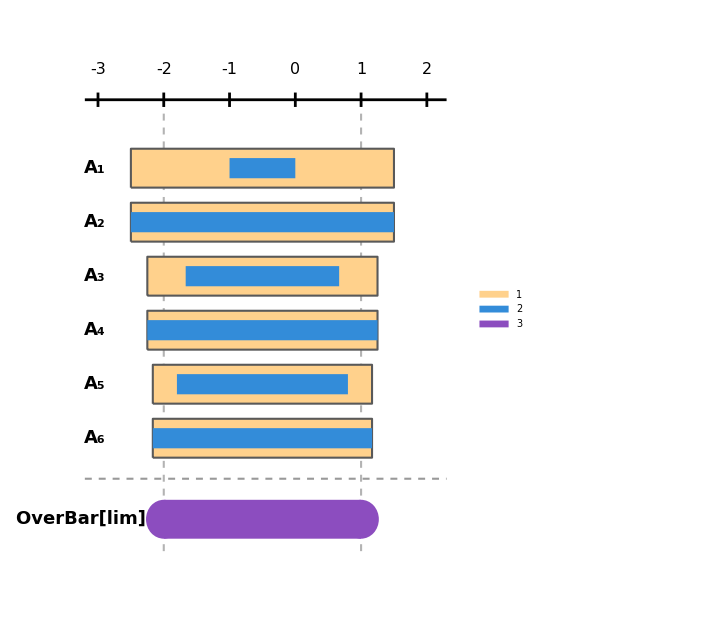

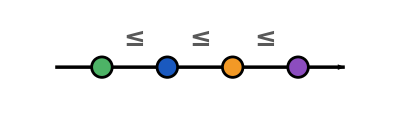
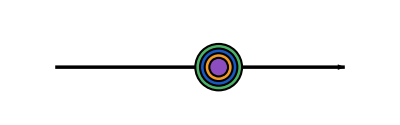
Apartados a) y b)
-Graphics-Apartado c)
-Graphics-

```mathematica
ClearAll[extIzq, extDer, mImp, deltaIzq, deltaDer, nMax, sep, hA, hD, colA, colD, colLiminf,
  filaA, yEje, yUlt, ySep, yLim, ejeReal, guias, separador, limite, grafico1, diagrama1];

extIzq[n_] := -2 - (-1)^n/n;    (* A_n = [extIzq, extDer] *)
extDer[n_] := 1 + (-1)^n/n;
mImp[n_] := If[OddQ[n], n, n + 1];   (* primer impar >= n *)
deltaIzq[n_] := -2 + 1/mImp[n];      (* delta_n = intersección de la cola *)
deltaDer[n_] := 1 - 1/mImp[n];

nMax = 6; sep = 0.75; hA = 0.27; hD = 0.14;
yEje = 0.95;

colA = RGBColor[0.78, 0.88, 1];
colD = RGBColor[0.1, 0.35, 0.75];
colLiminf = RGBColor[0.3, 0.7, 0.4];

(* cada fila: A_n (barra clara) con delta_n (barra oscura) dentro *)
filaA[n_] := With[{y = -(n - 1) sep}, {
    colA, EdgeForm[{GrayLevel[0.35], AbsoluteThickness[1.5]}],
    Rectangle[{extIzq[n], y - hA}, {extDer[n], y + hA}],
    colD, EdgeForm[None],
    Rectangle[{deltaIzq[n], y - hD}, {deltaDer[n], y + hD}],
    Black, Text[Style[Subscript["A", n], 18, Bold], {-3.05, y}, {1, 0}]}];

yUlt = -(nMax - 1) sep;
ySep = yUlt - 0.75 sep;
yLim = yUlt - 1.5 sep;

ejeReal = {Black, AbsoluteThickness[2], Line[{{-3.2, yEje}, {2.3, yEje}}],
   Table[{Line[{{k, yEje - 0.1}, {k, yEje + 0.1}}],
     Text[Style[k, 16], {k, yEje + 0.42}]}, {k, -3, 2}]};

guias = {GrayLevel[0.7], Dashed, AbsoluteThickness[1.5],
   Line[{{-2, yEje}, {-2, yLim - 0.5}}], Line[{{1, yEje}, {1, yLim - 0.5}}]};

separador = {GrayLevel[0.6], Dashed, AbsoluteThickness[1.5],
   Line[{{-3.2, ySep}, {2.3, ySep}}]};

(* liminf A_n = (-2, 1): extremos abiertos *)
limite = {
   colLiminf, EdgeForm[None], Rectangle[{-2, yLim - hA}, {1, yLim + hA}],
   White, Disk[{-2, yLim}, hA], colLiminf, AbsoluteThickness[3], Circle[{-2, yLim}, hA],
   White, Disk[{1, yLim}, hA], colLiminf, Circle[{1, yLim}, hA],
   Black, Text[Style[Row[{UnderBar["lim"], " ", Subscript["A", "n"]}], 18, Bold],
    {-3.05, yLim}, {1, 0}]};

grafico1 = Graphics[
   {guias, ejeReal, Table[filaA[n], {n, 1, nMax}], separador, limite},
   PlotRange -> {{-3.4, 2.5}, {yLim - 0.6, yEje + 0.6}}, ImageSize -> 520];

diagrama1 = Legended[grafico1,
   SwatchLegend[{colA, colD, colLiminf},
    {Subscript["A", "n"], Subscript["δ", "n"], Row[{UnderBar["lim"], " ", Subscript["A", "n"]}]},
    LabelStyle -> Directive[FontSize -> 17], LegendMarkerSize -> 20]];
ClearAll[extIzq, extDer, mPar, sigmaIzq, sigmaDer, nMax, sep, hA, hD, colS, colA2, colLimsup,
  filaS, yEje, yUlt, ySep, yLim, ejeReal, guias, separador, limite, grafico2, diagrama2];

extIzq[n_] := -2 - (-1)^n/n;
extDer[n_] := 1 + (-1)^n/n;
mPar[n_] := If[EvenQ[n], n, n + 1];   (* primer par >= n *)
sigmaIzq[n_] := -2 - 1/mPar[n];       (* sigma_n = unión de la cola *)
sigmaDer[n_] := 1 + 1/mPar[n];

nMax = 6; sep = 0.75; hA = 0.27; hD = 0.14;
yEje = 0.95;

colS = RGBColor[1, 0.82, 0.55];
colA2 = RGBColor[0.2, 0.55, 0.85];
colLimsup = RGBColor[0.55, 0.3, 0.75];

(* cada fila: sigma_n (barra ancha clara) con A_n (barra azul) dentro *)
filaS[n_] := With[{y = -(n - 1) sep}, {
    colS, EdgeForm[{GrayLevel[0.35], AbsoluteThickness[1.5]}],
    Rectangle[{sigmaIzq[n], y - hA}, {sigmaDer[n], y + hA}],
    colA2, EdgeForm[None],
    Rectangle[{extIzq[n], y - hD}, {extDer[n], y + hD}],
    Black, Text[Style[Subscript["A", n], 18, Bold], {-3.05, y}, {1, 0}]}];

yUlt = -(nMax - 1) sep;
ySep = yUlt - 0.75 sep;
yLim = yUlt - 1.5 sep;

ejeReal = {Black, AbsoluteThickness[2], Line[{{-3.2, yEje}, {2.3, yEje}}],
   Table[{Line[{{k, yEje - 0.1}, {k, yEje + 0.1}}],
     Text[Style[k, 16], {k, yEje + 0.42}]}, {k, -3, 2}]};

guias = {GrayLevel[0.7], Dashed, AbsoluteThickness[1.5],
   Line[{{-2, yEje}, {-2, yLim - 0.5}}], Line[{{1, yEje}, {1, yLim - 0.5}}]};

separador = {GrayLevel[0.6], Dashed, AbsoluteThickness[1.5],
   Line[{{-3.2, ySep}, {2.3, ySep}}]};

(* limsup A_n = [-2, 1]: extremos cerrados *)
limite = {
   colLimsup, EdgeForm[None], Rectangle[{-2, yLim - hA}, {1, yLim + hA}],
   Disk[{-2, yLim}, hA], Disk[{1, yLim}, hA],
   Black, Text[Style[Row[{OverBar["lim"], " ", Subscript["A", "n"]}], 18, Bold],
    {-3.05, yLim}, {1, 0}]};

grafico2 = Graphics[
   {guias, ejeReal, Table[filaS[n], {n, 1, nMax}], separador, limite},
   PlotRange -> {{-3.4, 2.5}, {yLim - 0.6, yEje + 0.6}}, ImageSize -> 520];

diagrama2 = Legended[grafico2,
   SwatchLegend[{colS, colA2, colLimsup},
    {Subscript["σ", "n"], Subscript["A", "n"], Row[{OverBar["lim"], " ", Subscript["A", "n"]}]},
    LabelStyle -> Directive[FontSize -> 17], LegendMarkerSize -> 20]];
ClearAll[colP, xs, ejeValores, panelOrden, panelConv, etiquetasLeyenda, columna1, columna2, diagrama3];

colP = {RGBColor[0.3, 0.7, 0.4], RGBColor[0.1, 0.35, 0.75],
   RGBColor[0.95, 0.6, 0.15], RGBColor[0.55, 0.3, 0.75]};
xs = {1, 2.4, 3.8, 5.2};

ejeValores[xMax_] := {Black, AbsoluteThickness[2.5], Arrowheads[0.05],
   Arrow[{{0, 0}, {xMax, 0}}]};

(* caso general: los cuatro valores en orden creciente *)
panelOrden = Graphics[{
    ejeValores[6.2],
    Table[{colP[[k]], EdgeForm[{Black, AbsoluteThickness[2]}], Disk[{xs[[k]], 0}, 0.22]}, {k, 1, 4}],
    Table[Text[Style["≤", 26, Bold, GrayLevel[0.35]],
      {(xs[[k]] + xs[[k + 1]])/2, 0.6}], {k, 1, 3}]},
   PlotRange -> {{-0.4, 6.6}, {-1, 1.2}}, ImageSize -> 400];

(* sucesión convergente: los cuatro valores coinciden en uno solo *)
panelConv = Graphics[{
    ejeValores[6.2],
    Table[{colP[[k]], EdgeForm[{Black, AbsoluteThickness[1.5]}],
      Disk[{3.5, 0}, 0.5 - 0.1 (k - 1)]}, {k, 1, 4}]},
   PlotRange -> {{-0.4, 6.6}, {-1, 1.2}}, ImageSize -> 400];

etiquetasLeyenda = {
   Row[{"μ(", UnderBar["lim"], " ", Subscript["A", "n"], ")"}],
   Row[{"liminf μ(", Subscript["A", "n"], ")"}],
   Row[{"limsup μ(", Subscript["A", "n"], ")"}],
   Row[{"μ(", OverBar["lim"], " ", Subscript["A", "n"], ")"}]};

columna1 = Column[{Style["Apartados a) y b)", 18, Bold], panelOrden},
   Alignment -> Center, Spacings -> 0.5];
columna2 = Column[{Style["Apartado c)", 18, Bold], panelConv},
   Alignment -> Center, Spacings -> 0.5];

diagrama3 = Legended[Row[{columna1, Spacer[40], columna2}],
   SwatchLegend[colP, etiquetasLeyenda,
    LabelStyle -> Directive[FontSize -> 17], LegendMarkerSize -> 20]];

diagrama1
diagrama2
diagrama3
```

```mathematica
Export[CloudObject["T2_3_a.png"], diagrama1, "PNG", Background -> None, ImageResolution -> 300, ImageSize -> 700]
Export[CloudObject["T2_3_b.png"], diagrama2, "PNG", Background -> None, ImageResolution -> 300, ImageSize -> 700]
Export[CloudObject["T2_3_c.png"], diagrama3, "PNG", Background -> None, ImageResolution -> 300, ImageSize -> 700]
```

CloudObject[https://www.wolframcloud.com/obj/jesusparejop/T2_3_a.png]

CloudObject[https://www.wolframcloud.com/obj/jesusparejop/T2_3_b.png]

CloudObject[https://www.wolframcloud.com/obj/jesusparejop/T2_3_c.png]